```mathematica
r={x[t]+L0 Sin[θ[t]]Cos[ϕ[t]],L0 Sin[θ[t]]Sin[ϕ[t]],L0 Cos[θ[t]]};
v=D[r,t];
T1=1/2 m Total[v^2];
T2=1/6 M x'[t]^2;
V=m g L0 Cos[θ[t]];
W=F^2/(4 IC EC l^2);

F=(3 EC IC  x[t])/l^3;

IC = (π d^4)/32;
Lagrange=(T1+T2-V-W)*ⅇ^(0.01t);

Eqn1 = D[D[Lagrange,x'[t]],t]-D[Lagrange,x[t]]==0;
Eqn2=D[D[Lagrange,θ'[t]],t]-D[Lagrange,θ[t]]== 0;
Eqn3=D[D[Lagrange,ϕ'[t],t]-D[Lagrange,ϕ[t]]]== 0;
```

-Graphics3D-

-Graphics-

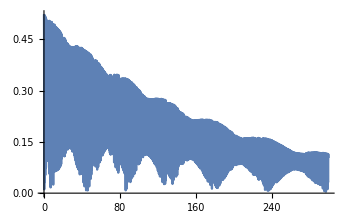

```mathematica
{m ,M,L0,l,d,EC,g}= {0.0314,0.01378,0.3,0.3675,0.005,0.8*10^8,9.8};

sol=NDSolve[{Eqn1,Eqn2,Eqn3,x[0]==0,x'[0]==0,ϕ[0]==1.472,ϕ'[0]==0,θ[0]==150Degree,θ'[0]==0},{x[t],ϕ[t],θ[t]},{t,0,500}];
data=sol[[1]];
xdata=data[[1,2]];
dxdata = D[xdata,t];
faidata=data[[2,2]];
dfaidata=D[dfaidata,t];
thetadata=data[[3,2]];
dthetadata=D[thetadata,t];
ldata = xdata/Cos[faidata];
dldata = D[ldata,t];
rdata = r/.sol[[1]];
drdata=D[rdata,t];
ParametricPlot3D[r/.sol[[1]],{t,0,200},Axes->False,PlotStyle->Blue,PlotPoints->999]
ParametricPlot[{dthetadata,thetadata},{t,0,500},AspectRatio->1,AxesLabel->Automatic,PlotPoints->9999,PlotTheme->"Detailed",PlotRange->Full]
ParametricPlot[{dfaidata,faidata},{t,0,300},AspectRatio->1,PlotRange->0.5,AxesLabel->Automatic];
ParametricPlot[{dldata,ldata},{t,0,200},AspectRatio->1];
Plot[Pi-thetadata,{t,0,300}]
```